| Wert | Fehler
Steigung b | -0.00543329 | 0.000244256
Achsenabschnitt a | 1.89644 | 0.0254014
R^2 | 0.999096 | 
Χ^2/(n - 2) | 0.56366 |

{b→-0.00543329,Δb→0.000244256,a→1.89644,Δa→0.0254014}

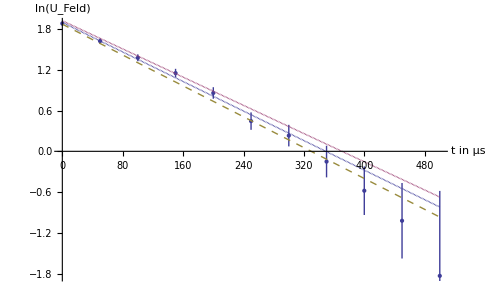

```mathematica
Needs["ErrorBarPlots`"]

LinReg[data_]:=Module[{x,y,Δy,S,a0,b0,Δa0,Δb0,n,ybar, Nom, DeNom, R,Χ},
n=Length[data];
x=data[[All, 1]];
y=data[[All, 2]];
Δy=data[[All, 3]];

S=Sum[1/(Δy[[i]])^2,{i,n}]*Sum[(x[[i]])^2/(Δy[[i]])^2,{i,n}]-(Sum[x[[i]]/(Δy[[i]])^2,{i,n}])^2;

a0=1/S*(Sum[(x[[i]])^2/(Δy[[i]])^2,{i,n}]*Sum[y[[i]]/(Δy[[i]])^2,{i,n}]-Sum[x[[i]]/(Δy[[i]])^2,{i,n}]*Sum[x[[i]]*y[[i]]/(Δy[[i]])^2,{i,n}]);

b0=1/S*(Sum[1/(Δy[[i]])^2,{i,n}]*Sum[x[[i]]*y[[i]]/(Δy[[i]])^2,{i,n}]-Sum[x[[i]]/(Δy[[i]])^2,{i,n}]*Sum[y[[i]]/(Δy[[i]])^2,{i,n}]);

Δa0=Sqrt[1/S*Sum[(x[[i]])^2/(Δy[[i]])^2,{i,n}]];
Δb0=Sqrt[1/S*Sum[1/(Δy[[i]])^2,{i,n}]];
ybar=1/n*(∑_(i=1)^n y[[i]]/Δy[[i]]^2)/(∑_(i=1)^n 1/Δy[[i]]^2);
Nom =∑_(i=1)^n (y[[i]]-(a0+b0*x[[i]]))^2/Δy[[i]]^2;
DeNom=∑_(i=1)^n (y[[i]]-ybar)^2/Δy[[i]]^2;
R= √(1- Nom/DeNom);
;
Χ=√(∑_(i=1)^n ((y[[i]]-(a0+b0*x[[i]]))/Δy[[i]])^2);

(*Aufgabe 1a).*)
Print[TableForm[{{"","Wert","Fehler"},{"Steigung b",b0,Δb0},{"Achsenabschnitt a",a0,Δa0}, {"R^2", R^2, ""}, {"Χ^2/(n - 2)",Χ^2/(n-2),""}}]];
{b-> b0,Δb->Δb0, a->a0,Δa->Δa0}

]

aufgabe3b[data_]:=Module[{x,y,f,S,s,a0,b0,Δa0,Δb0,n,ybar, Nom, DeNom, R,Χ},
n=Length[data];
x=data[[All, 1]];
y=data[[All, 2]];
f=data[[All, 3]];

S= (∑_(i=1)^n 1/f⟦i⟧^2)*(∑_(i=1)^n x⟦i⟧^2/f⟦i⟧^2)-(∑_(i=1)^n x⟦i⟧/f⟦i⟧^2)^2;

a0=1/S((∑_(i=1)^n x⟦i⟧^2/f⟦i⟧^2)*(∑_(i=1)^n y⟦i⟧/f⟦i⟧^2)-(∑_(i=1)^n x⟦i⟧/f⟦i⟧^2)*(∑_(i=1)^n (x⟦i⟧*y⟦i⟧)/f⟦i⟧^2));

b0=1/S((∑_(i=1)^n 1/f⟦i⟧^2)*(∑_(i=1)^n (x⟦i⟧*y⟦i⟧)/f⟦i⟧^2)-(∑_(i=1)^n x⟦i⟧/f⟦i⟧^2)*(∑_(i=1)^n y⟦i⟧/f⟦i⟧^2));
Χ=√(∑_(i=1)^n ((y[[i]]-(a0+b0*x[[i]]))/f[[i]])^2);
s=√(Χ^2/(n-2));

Δa0=√(1/S*∑_(i=1)^n x⟦i⟧^2/f⟦i⟧^2*s^2);
Δb0=√(1/S*∑_(i=1)^n 1/f⟦i⟧^2*s^2);
ybar=1/n*(∑_(i=1)^n y[[i]]/Δy[[i]]^2)/(∑_(i=1)^n 1/Δy[[i]]^2);
Nom =∑_(i=1)^n (y[[i]]-(a0+b0*x[[i]]))^2/Δy[[i]]^2;
DeNom=∑_(i=1)^n (y[[i]]-ybar)^2/Δy[[i]]^2;
R= √(1- Nom/DeNom);

Print[TableForm[{{"","Wert","Fehler"},{"Steigung b",b0,Δb0},{"Achsenabschnitt a",a0,Δa0},{"Anzahl der Messwerte", n,""}, {"Bestimmtheitsmaß R^2", R^2, ""}, {"Die Größe Χ^2/(n - 2)",Χ^2/(n-2),""}}]];
{b-> b0,Δb->Δb0, a->a0,Δa->Δa0}

]
aufgabe4b[data_]:=Module[{x,y,Δy,s,a0,b0,Δa0,Δb0,n,ybar, Nom, DeNom, R,Χ},
n=Length[data];
x=data[[All, 1]];
y=data[[All, 2]];
Δy=data[[All, 3]];

Δa0=0;
a0=0;

b0=(∑_(i=1)^n ((x⟦i⟧*y⟦i⟧)/Δy⟦i⟧^2))/(∑_(i=1)^n (x⟦i⟧^2/Δy⟦i⟧^2));
Χ=√(∑_(i=1)^n ((y[[i]]-b0*x[[i]])/Δy[[i]])^2);
s=√(Χ^2/(n-2));

Δb0=√(1/(∑_(j=1)^n x⟦j⟧^2/Δy⟦j⟧^2));
ybar=1/n*(∑_(i=1)^n y[[i]]/Δy[[i]]^2)/(∑_(i=1)^n 1/Δy[[i]]^2);
Nom =∑_(i=1)^n (y[[i]]-(a0+b0*x[[i]]))^2/Δy[[i]]^2;
DeNom=∑_(i=1)^n (y[[i]]-ybar)^2/Δy[[i]]^2;
R= √(1- Nom/DeNom);

Print[TableForm[{{"","Wert","Fehler"},{"Steigung b",b0,Δb0},{"Achsenabschnitt a",a0,Δa0},{"Anzahl der Messwerte", n,""}, {"Bestimmtheitsmaß R^2", R^2, ""}, {"Die Größe Χ^2/(n - 2)",Χ^2/(n-2),""}}]];
{b-> b0,Δb->Δb0, a->a0,Δa->Δa0}

]

(*Aufgabe 1b).*)
linear=ReadList["~/gp2/tra/graphen/tab_2.2.1.tsv",{Real, Real, Real}];
regerg=LinReg[linear]
Show[ErrorListPlot[linear, AxesLabel->{"t in μs", "ln(U_Feld)"}],
Plot[Evaluate[
{b*t+a,(b+Δb)*t+a+Δa,(b-Δb)*t+a-Δa}/.regerg],{t,0,500},
PlotStyle->{Dashing[{.0}],Dashing[{0.001}], Dashing[{.01}]}]]
```